```mathematica
Table[i+j, {i,1,10}, {j,1,10}]
```

{{2,3,4,5,6,7,8,9,10,11},{3,4,5,6,7,8,9,10,11,12},{4,5,6,7,8,9,10,11,12,13},{5,6,7,8,9,10,11,12,13,14},{6,7,8,9,10,11,12,13,14,15},{7,8,9,10,11,12,13,14,15,16},{8,9,10,11,12,13,14,15,16,17},{9,10,11,12,13,14,15,16,17,18},{10,11,12,13,14,15,16,17,18,19},{11,12,13,14,15,16,17,18,19,20}}

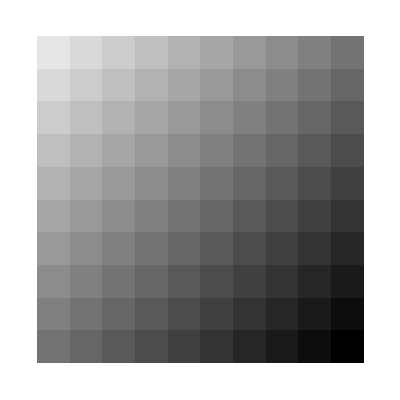

```mathematica
ArrayPlot[%]
```

```mathematica
Manipulate[ArrayPlot[Table[i+j,{i,1,m},{j,1,m}]],{m,3,100,1}]
```

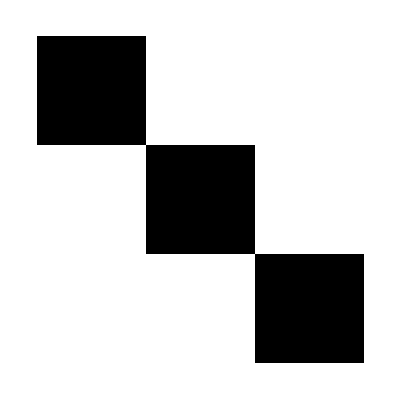

```mathematica
ArrayPlot[Table[If[i==j, 1,0],{i,1,3},{j,1,3}]]
```

```mathematica
Manipulate[ArrayPlot[Table[If[i+j-1==m, 1,0],{i,1,m},{j,1,m}]],{m,3,10,1}]
```

```mathematica
diagonalMatrix[m_]:=Table[If[i==j,1,0],{i,1,m},{j,1,m}]
antiDiagonalMatrix[m_]:=Table[If[i+j-1==m,1,0],{i,1,m},{j,1,m}]
```

```mathematica
Manipulate[{ArrayPlot[IdentityMatrix[m]], ArrayPlot[antiDiagonalMatrix[m]], ArrayPlot[IdentityMatrix[m] * antiDiagonalMatrix[m]]},{m,3,100,1}]
```

```mathematica
Manipulate[{ArrayPlot[antiDiagonalMatrix[m]], ArrayPlot[antiDiagonalMatrix[m]], ArrayPlot[Dot[diagonalMatrix[m] , diagonalMatrix[m]]]},{m,3,100,1}]
```

```mathematica
xMatrix[m_]:=Table[If[Abs[((i/100)-0.5)^2-(j/100)+0.5 ]<= 0.01,1,0],{i,1,m},{j,1,m}]
ArrayPlot[xMatrix[100]]
```

-Graphics-

```mathematica
yMatrix[m_]:=Table[If[Abs[ 1-((j/100)-0.5)^2-(i/100)- 0.5 ]<= 0.01,1,0],{i,1,m},{j,1,m}]
ArrayPlot[yMatrix[100]]
```

-Graphics-

```mathematica
Manipulate[{ArrayPlot[xMatrix[m]],ArrayPlot[yMatrix[m]], ArrayPlot[yMatrix[m] * xMatrix[m]]}, {m,100,500}]
```

```mathematica
aRange = 1.5;
uRange=aRange;
lRange=- aRange;
resolution=50;
tol = 0.05;
```

```mathematica
(*Define a struct-like object for dimensions*)
dimStruct[lower_,upper_,resolution_]:={lower,upper,resolution};

(*Function to create a matrix based on a function*)
makeMat[f_,xdim_,ydim_,tol_]:=Module[{rows=xdim[[3]],cols=ydim[[3]],xstep,ystep,result},result=ConstantArray[False,{rows,cols}];
xstep=(xdim[[2]]-xdim[[1]])/xdim[[3]];
ystep=(ydim[[2]]-ydim[[1]])/ydim[[3]];
Do[xval=xdim[[1]]+(i-0.5)*xstep;
yval=ydim[[1]]+(j-0.5)*ystep;
result[[i,j]]=If[Abs[f[xval,yval]]<tol,1,0],{i,1,rows},{j,1,cols}];
result]

(* Declare some parameters *)
aRange = 1.5;
uRange=aRange;
lRange=- aRange;
resolution=1500;
tol = 0.05;

(*Define dimensions*)
dim=dimStruct[lRange,uRange,resolution];

(*Create matrices*)
M1=makeMat[(#2-#1^2&),dim,dim,tol];
M2=makeMat[(#1+#2^2 - 1 &),dim,dim,tol]; (*Assuming a similar function for M2*)

(*Visualize matrices using ArrayPlot*)
{ArrayPlot[M1,ColorRules->{0->White,1->Black}], ArrayPlot[M2,ColorRules->{0->White,1->Black}],ArrayPlot[M1 . M2,ColorRules->{0->White,1->Black}]}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
M1. M2 //MatrixForm
```

```mathematica
M1 *  M2 //MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Dot[M1, M2]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)